```mathematica
sec02inclass = {63, 87, 80, 72, 79, 62, 56, 66, 82, 61, 77, 43, 76, 64, 57, 56, 83, 50, 56}
```

{63,87,80,72,79,62,56,66,82,61,77,43,76,64,57,56,83,50,56}

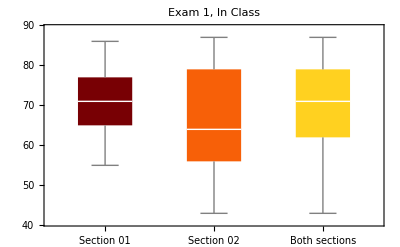

```mathematica
BoxWhiskerChart[{sec01inclass, sec02inclass, Union[sec01inclass, sec02inclass]},ChartLabels->{"Section 01", "Section 02", "Both sections"}, ChartStyle-> "SolarColors" , PlotLabel->"Exam 1, In Class"]
```

```mathematica
sec01inclass = {84, 65, 73, 71, 75, 65, 69, 83, 57, 74, 69, 55, 67, 86, 77, 60, 74, 60, 85}
```

{84,65,73,71,75,65,69,83,57,74,69,55,67,86,77,60,74,60,85}

```mathematica
allinclass =
```

```mathematica
sec02all = {63, 87, 90, 82, 79, 72, 66, 76, 92, 71, 87, 53, 86, 74, 67, 66, 93, 60, 66}
```

{63,87,90,82,79,72,66,76,92,71,87,53,86,74,67,66,93,60,66}

```mathematica
sec01all = {95, 94, 75, 83, 81, 85, 75, 79, 93, 67, 84, 79, 65, 77, 96, 87, 60, 84, 70}
```

{95,94,75,83,81,85,75,79,93,67,84,79,65,77,96,87,60,84,70}

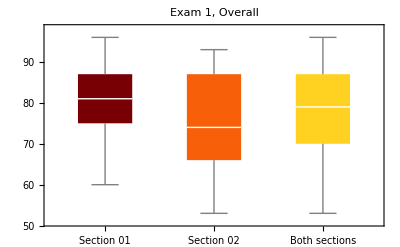

```mathematica
BoxWhiskerChart[{sec01all, sec02all, Union[sec01all, sec02all]},ChartLabels->{"Section 01", "Section 02", "Both sections"}, ChartStyle-> "SolarColors" , PlotLabel->"Exam 1, Overall"]
```

```mathematica
N[Mean[sec01all]]
```

80.4737

```mathematica
N[Mean[sec02all]]
```

75.2632

```mathematica
N[Mean[Union[sec01all, sec02all]]]
```

78.3704